```mathematica
ClearAll["Global`*"]
```

```mathematica
Cp[d1]:=Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2)))
```

```mathematica
D[Cp[d1],d1]//FullSimplify
```

(Gamma[(1 + d1)/2]*(-1 - (-2 + d1)*PolyGamma[0, d1/2] + (-2 + d1)*PolyGamma[0, (1 + d1)/2]))/(2*(-2 + d1)^(3/2)*Sqrt[Pi]*Gamma[d1/2])

```mathematica
D[Cp[d1],{d1,2}]//FullSimplify
```

(1/(4*(-2 + d1)^(5/2)*Sqrt[Pi]*Gamma[d1/2]))*(Gamma[(1 + d1)/2]*(3 + (-2 + d1)^2*PolyGamma[0, d1/2]^2 - 2*(-2 + d1)*PolyGamma[0, (1 + d1)/2] + 
    (-2 + d1)^2*PolyGamma[0, (1 + d1)/2]^2 + 2*(-2 + d1)*PolyGamma[0, d1/2]*(1 - (-2 + d1)*PolyGamma[0, (1 + d1)/2]) - 
    (-2 + d1)^2*PolyGamma[1, d1/2] + (-2 + d1)^2*PolyGamma[1, (1 + d1)/2]))

```mathematica
Ap[d1,d2]:=4 d2 Cp[d1] (d1-2)/(d1-1)
```

```mathematica
D[Ap[d1,d2],d1]//FullSimplify
```

(2*d2*Gamma[(1 + d1)/2]*(3 - d1 - (-2 + d1)*(-1 + d1)*PolyGamma[0, d1/2] + (-2 + d1)*(-1 + d1)*PolyGamma[0, (1 + d1)/2]))/
  (Sqrt[-2 + d1]*(-1 + d1)^2*Sqrt[Pi]*Gamma[d1/2])

```mathematica
D[Ap[d1,d2],{d1,2}]//FullSimplify
```

(1/((1 - d1)^3*(-2 + d1)^(3/2)*Sqrt[Pi]*Gamma[d1/2]))*(d2*Gamma[(1 + d1)/2]*
   (-23 + 18*d1 - 3*d1^2 + 2*(-3 + d1)*(-2 + d1)*(-1 + d1)*(-PolyGamma[0, d1/2] + PolyGamma[0, (1 + d1)/2]) - 
    (-2 + d1)^2*(-1 + d1)^2*((PolyGamma[0, d1/2] - PolyGamma[0, (1 + d1)/2])^2 - PolyGamma[1, d1/2] + PolyGamma[1, (1 + d1)/2])))

```mathematica
D[Ap[d1,d2],d2]//FullSimplify
```

(4*Gamma[(1/2)*(-1 + d1)])/(Sqrt[-2 + d1]*Sqrt[Pi]*Gamma[-1 + d1/2])

```mathematica
D[Ap[d1,d2],{d2,2}]//FullSimplify
```

0

```mathematica
D[Ap[d1,d2],d1,d2]//FullSimplify
```

(2*Gamma[(1 + d1)/2]*(3 - d1 - (-2 + d1)*(-1 + d1)*PolyGamma[0, d1/2] + (-2 + d1)*(-1 + d1)*PolyGamma[0, (1 + d1)/2]))/
  (Sqrt[-2 + d1]*(-1 + d1)^2*Sqrt[Pi]*Gamma[d1/2])

```mathematica
Bp[d1,d2]:=√(1+3 d2^2-Ap[d1,d2]^2)
```

```mathematica
D[Bp[d1,d2],d1]//FullSimplify
```

(8*d2^2*Gamma[(1 + d1)/2]^2*(-3 + d1 + (-2 + d1)*(-1 + d1)*PolyGamma[0, d1/2] - (-2 + d1)*(-1 + d1)*PolyGamma[0, (1 + d1)/2]))/
  ((-1 + d1)^3*Sqrt[Pi]*Sqrt[Pi + 3*d2^2*Pi - (4*(-2 + d1)*d2^2*Gamma[(1/2)*(-1 + d1)]^2)/Gamma[d1/2]^2]*Gamma[d1/2]^2)

```mathematica
D[Bp[d1,d2],{d1,2}]//Simplify
```

-((4*(16*d2^4*Gamma[(1 + d1)/2]^4*(-3 + d1 + (2 - 3*d1 + d1^2)*PolyGamma[0, d1/2] - (2 - 3*d1 + d1^2)*PolyGamma[0, (1 + d1)/2])^2 + 
     d2^2*Gamma[(1 + d1)/2]^2*((-1 + d1)^2*Pi*Gamma[d1/2]^2 + 3*(-1 + d1)^2*d2^2*Pi*Gamma[d1/2]^2 - 16*(-2 + d1)*d2^2*Gamma[(1 + d1)/2]^2)*
      (8 + 12*(-2 + d1) - 8*d1 + 8*(-2 + d1)*(-1 + d1)*PolyGamma[0, d1/2] - 4*(-1 + d1)^2*PolyGamma[0, d1/2] + 
       2*(-2 + d1)*(-1 + d1)^2*PolyGamma[0, d1/2]^2 - 8*(-2 + d1)*(-1 + d1)*PolyGamma[0, (1 + d1)/2] + 
       4*(-1 + d1)^2*PolyGamma[0, (1 + d1)/2] - 4*(-2 + d1)*(-1 + d1)^2*PolyGamma[0, d1/2]*PolyGamma[0, (1 + d1)/2] + 
       2*(-2 + d1)*(-1 + d1)^2*PolyGamma[0, (1 + d1)/2]^2 - (-2 + d1)*(-1 + d1)^2*PolyGamma[1, d1/2] + 
       (-2 + d1)*(-1 + d1)^2*PolyGamma[1, (1 + d1)/2])))/((-1 + d1)^6*Pi^2*Gamma[d1/2]^4*
    (1 + 3*d2^2 - (16*(-2 + d1)*d2^2*Gamma[(1 + d1)/2]^2)/((-1 + d1)^2*Pi*Gamma[d1/2]^2))^(3/2)))

```mathematica
D[Bp[d1,d2],d2]//FullSimplify
```

(6 d2-(8 (-2+d1) d2 Gamma[1/2 (-1+d1)]^2)/(π Gamma[d1/2]^2))/(2 √(1+3 d2^2-(4 (-2+d1) d2^2 Gamma[1/2 (-1+d1)]^2)/(π Gamma[d1/2]^2)))

```mathematica
D[Bp[d1,d2],{d2,2}]//FullSimplify
```

(3*(-1 + d1)^2*Pi*Gamma[d1/2]^2 - 16*(-2 + d1)*Gamma[(1 + d1)/2]^2)/
  (Sqrt[1 + 3*d2^2 - (4*(-2 + d1)*d2^2*Gamma[(1/2)*(-1 + d1)]^2)/(Pi*Gamma[d1/2]^2)]*((-1 + d1)^2*(1 + 3*d2^2)*Pi*Gamma[d1/2]^2 - 
    16*(-2 + d1)*d2^2*Gamma[(1 + d1)/2]^2))

```mathematica
D[Bp[d1,d2],d1,d2]//ExpandAll//Simplify//FullSimplify
```

(32 d2 ((-1+d1)^2 (2+3 d2^2) π^2 Gamma[d1]^2-4^(1+d1) (-2+d1) d2^2 Gamma[(1+d1)/2]^4) (-3+d1+(-2+d1) (-1+d1) PolyGamma[0,d1/2]-(-2+d1) (-1+d1) PolyGamma[0,(1+d1)/2]))/((-1+d1)^5 π^(3/2) √(π+3 d2^2 π-(4 (-2+d1) d2^2 Gamma[1/2 (-1+d1)]^2)/Gamma[d1/2]^2) (-64 (-2+d1) d2^2 Gamma[-1+d1]^2+4^d1 (1+3 d2^2) Gamma[d1/2]^4))

```mathematica
𝒟=Piecewise[{{Log[(Bp[d1,d2] Cp[d1])/σ (1+(Bp[d1,d2] ((x-μ)/σ) +Ap[d1,d2])^2/((1-d2)^2(d1-2)))^(-(1+d1)/2)],x<μ-Ap[d1,d2]/Bp[d1,d2] σ},{Log[(Bp[d1,d2] Cp[d1])/σ (1+(Bp[d1,d2] ((x-μ)/σ) +Ap[d1,d2])^2/((1+d2)^2(d1-2)))^(-(1+d1)/2)],x≥ μ-Ap[d1,d2]/Bp[d1,d2] σ}}]
```

Piecewise[{{Log[(Bp[d1,d2] (1+(Ap[d1,d2]+((x-μ) Bp[d1,d2])/σ)^2/((-2+d1) (1-d2)^2))^(1/2 (-1-d1)) Cp[d1])/σ], x<μ-(σ Ap[d1,d2])/Bp[d1,d2]}, {Log[(Bp[d1,d2] (1+(Ap[d1,d2]+((x-μ) Bp[d1,d2])/σ)^2/((-2+d1) (1+d2)^2))^(1/2 (-1-d1)) Cp[d1])/σ], x≥μ-(σ Ap[d1,d2])/Bp[d1,d2]}, {0, True}}]

```mathematica
D[𝒟,μ]/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{(B*(1 + d1)*(A*sigma + B*(-mu + x)))/((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x)), 
    (A*sigma)/B + x < mu}, {(B*(1 + d1)*(A*sigma + B*(-mu + x)))/((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 
      2*A*B*sigma*(-mu + x)), (A*sigma)/B + x >= mu}}, 0]

```mathematica
D[𝒟,{μ,2}]/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{(B^2*(1 + d1)*((A^2 - (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x)))/
     ((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))^2, (A*sigma)/B + x < mu}, 
   {(B^2*(1 + d1)*((A^2 - (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x)))/
     ((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))^2, (A*sigma)/B + x >= mu}}, 0]

```mathematica
D[𝒟,μ,d1]/.{Ap[d1,d2]->Ap,Bp[d1,d2]->Bp,Cp[d1]->Cp}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{(Bp*(Bp*(x - μ) + Ap*σ)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - 3*(-1 + d2)^2)*σ^2) + 
      (1 + d1)*σ*((-Bp)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - (-2 + d1)*(-1 + d2)^2)*σ^2)*Derivative[1, 0][Ap][d1, d2] + 
        (Ap*Bp^2*(x - μ)^2 + 2*Bp*(Ap^2 + (-2 + d1)*(-1 + d2)^2)*(x - μ)*σ + Ap*(Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)*
         Derivative[1, 0][Bp][d1, d2]))/(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)^2, x + (Ap*σ)/Bp < μ}, 
   {(Bp*(Bp*(x - μ) + Ap*σ)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - 3*(1 + d2)^2)*σ^2) + 
      (1 + d1)*σ*((-Bp)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - (-2 + d1)*(1 + d2)^2)*σ^2)*Derivative[1, 0][Ap][d1, d2] + 
        (Ap*Bp^2*(x - μ)^2 + 2*Bp*(Ap^2 + (-2 + d1)*(1 + d2)^2)*(x - μ)*σ + Ap*(Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)*
         Derivative[1, 0][Bp][d1, d2]))/(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)^2, 
    x + (Ap*σ)/Bp >= μ}}, 0]

```mathematica
D[𝒟,μ,d2]/.{Ap[d1,d2]->Ap,Bp[d1,d2]->Bp,Cp[d1]->Cp}//ExpandAll//Simplify//FullSimplify
```

Piecewise[
  {{-(((1 + d1)*σ*(2*Bp*(-2 + d1)*(-1 + d2)*σ*(Bp*x - Bp*μ + Ap*σ) + Bp*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + 
          (Ap^2 - (-2 + d1)*(-1 + d2)^2)*σ^2)*Derivative[0, 1][Ap][d1, d2] - 
        (Ap*Bp^2*(x - μ)^2 + 2*Bp*(Ap^2 + (-2 + d1)*(-1 + d2)^2)*(x - μ)*σ + Ap*(Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)*
         Derivative[0, 1][Bp][d1, d2]))/(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)^2), 
    x + (Ap*σ)/Bp < μ}, 
   {-(((1 + d1)*σ*(2*Bp*(-2 + d1)*(1 + d2)*σ*(Bp*x - Bp*μ + Ap*σ) + Bp*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + 
          (Ap^2 - (-2 + d1)*(1 + d2)^2)*σ^2)*Derivative[0, 1][Ap][d1, d2] - 
        (Ap*Bp^2*(x - μ)^2 + 2*Bp*(Ap^2 + (-2 + d1)*(1 + d2)^2)*(x - μ)*σ + Ap*(Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)*
         Derivative[0, 1][Bp][d1, d2]))/(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)^2), 
    x + (Ap*σ)/Bp >= μ}}, 0]

```mathematica
D[𝒟,μ,σ]/.{Ap[d1,d2]->Ap,Bp[d1,d2]->Bp,Cp[d1]->Cp,μ->mu,σ->sigma}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{-((Bp*(1 + d1)*(Ap^3*sigma^2 + Ap*(-2 + d1)*(-1 + d2)^2*sigma^2 - 2*Bp*(-2 + d1)*(-1 + d2)^2*sigma*(mu - x) + Ap*Bp^2*(mu - x)^2 + 
        2*Ap^2*Bp*sigma*(-mu + x)))/((Ap^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + Bp^2*(mu - x)^2 + 2*Ap*Bp*sigma*(-mu + x))^2), 
    (Ap*sigma)/Bp + x < mu}, {-((Bp*(1 + d1)*(Ap^3*sigma^2 + Ap*(-2 + d1)*(1 + d2)^2*sigma^2 - 2*Bp*(-2 + d1)*(1 + d2)^2*sigma*(mu - x) + 
        Ap*Bp^2*(mu - x)^2 + 2*Ap^2*Bp*sigma*(-mu + x)))/((Ap^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + Bp^2*(mu - x)^2 + 2*Ap*Bp*sigma*(-mu + x))^
       2), (Ap*sigma)/Bp + x >= mu}}, 0]

```mathematica
Integrate[𝒟,{x,-∞,y},Assumptions->{d1>2,d2<1,d2>-1,Cp∈Reals,y∈Reals,Ap∈Reals,Bp∈Reals,μ∈Reals,σ∈Reals,σ>0,x∈Reals}]
```

$Aborted

```mathematica
D[𝒟,σ]/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{((-(A^2 + (-2 + d1)*(-1 + d2)^2))*sigma^2 - A*B*(-1 + d1)*sigma*(mu - x) + B^2*d1*(mu - x)^2)/
     (sigma*((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))), (A*sigma)/B + x < mu}, 
   {((-(A^2 + (-2 + d1)*(1 + d2)^2))*sigma^2 - A*B*(-1 + d1)*sigma*(mu - x) + B^2*d1*(mu - x)^2)/
     (sigma*((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))), (A*sigma)/B + x >= mu}}, 0]

```mathematica
D[𝒟,{σ,2}]/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{((A^2 + (-2 + d1)*(-1 + d2)^2)^2*sigma^4 + 2*A*B*(-1 + d1)*(A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^3*(mu - x) - 
      B^2*(A^2*(-1 + 5*d1) + (-2 + d1)*(1 + 3*d1)*(-1 + d2)^2)*sigma^2*(mu - x)^2 + 4*A*B^3*d1*sigma*(mu - x)^3 - B^4*d1*(mu - x)^4)/
     (sigma^2*((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))^2), (A*sigma)/B + x < mu}, 
   {((A^2 + (-2 + d1)*(1 + d2)^2)^2*sigma^4 + 2*A*B*(-1 + d1)*(A^2 + (-2 + d1)*(1 + d2)^2)*sigma^3*(mu - x) - 
      B^2*(A^2*(-1 + 5*d1) + (-2 + d1)*(1 + 3*d1)*(1 + d2)^2)*sigma^2*(mu - x)^2 + 4*A*B^3*d1*sigma*(mu - x)^3 - B^4*d1*(mu - x)^4)/
     (sigma^2*((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))^2), (A*sigma)/B + x >= mu}}, 0]

```mathematica
D[𝒟,σ,d1]/.{Ap[d1,d2]->Ap,Bp[d1,d2]->Bp,Cp[d1]->Cp,μ->mu,σ->sigma}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{((x - μ)*(Bp*(Bp*(x - μ) + Ap*σ)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - 3*(-1 + d2)^2)*σ^2) + 
       (1 + d1)*σ*((-Bp)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - (-2 + d1)*(-1 + d2)^2)*σ^2)*Derivative[1, 0][Ap][d1, d2] + 
         (Ap*Bp^2*(x - μ)^2 + 2*Bp*(Ap^2 + (-2 + d1)*(-1 + d2)^2)*(x - μ)*σ + Ap*(Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)*
          Derivative[1, 0][Bp][d1, d2])))/(σ*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)^2), 
    x + (Ap*σ)/Bp < μ}, {((x - μ)*(Bp*(Bp*(x - μ) + Ap*σ)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - 3*(1 + d2)^2)*σ^2) + 
       (1 + d1)*σ*((-Bp)*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 - (-2 + d1)*(1 + d2)^2)*σ^2)*Derivative[1, 0][Ap][d1, d2] + 
         (Ap*Bp^2*(x - μ)^2 + 2*Bp*(Ap^2 + (-2 + d1)*(1 + d2)^2)*(x - μ)*σ + Ap*(Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)*
          Derivative[1, 0][Bp][d1, d2])))/(σ*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)^2), 
    x + (Ap*σ)/Bp >= μ}}, 0]

```mathematica
D[𝒟,σ,d2]/.{Ap[d1,d2]->Ap,Bp[d1,d2]->Bp,Cp[d1]->Cp,μ->mu,σ->sigma}//ExpandAll//Simplify//FullSimplify
```

Piecewise[{{-(((1 + d1)*(mu - x)*(2*Bp*(-2 + d1)*(-1 + d2)*sigma*((-Ap)*sigma + Bp*(mu - x)) - 
        Bp*((Ap^2 - (-2 + d1)*(-1 + d2)^2)*sigma^2 + Bp^2*(mu - x)^2 + 2*Ap*Bp*sigma*(-mu + x))*Derivative[0, 1][Ap][d1, d2] + 
        (Ap^3*sigma^2 + Ap*(-2 + d1)*(-1 + d2)^2*sigma^2 + Ap*Bp^2*(mu - x)^2 + 2*Ap^2*Bp*sigma*(-mu + x) + 
          2*Bp*(-2 + d1)*(-1 + d2)^2*sigma*(-mu + x))*Derivative[0, 1][Bp][d1, d2]))/
      ((Ap^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + Bp^2*(mu - x)^2 + 2*Ap*Bp*sigma*(-mu + x))^2), (Ap*sigma)/Bp + x < mu}, 
   {-(((1 + d1)*(mu - x)*(2*Bp*(-2 + d1)*(1 + d2)*sigma*((-Ap)*sigma + Bp*(mu - x)) - 
        Bp*((Ap^2 - (-2 + d1)*(1 + d2)^2)*sigma^2 + Bp^2*(mu - x)^2 + 2*Ap*Bp*sigma*(-mu + x))*Derivative[0, 1][Ap][d1, d2] + 
        (Ap^3*sigma^2 + Ap*(-2 + d1)*(1 + d2)^2*sigma^2 - 2*Bp*(-2 + d1)*(1 + d2)^2*sigma*(mu - x) + Ap*Bp^2*(mu - x)^2 + 
          2*Ap^2*Bp*sigma*(-mu + x))*Derivative[0, 1][Bp][d1, d2]))/((Ap^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + Bp^2*(mu - x)^2 + 
        2*Ap*Bp*sigma*(-mu + x))^2), (Ap*sigma)/Bp + x >= mu}}, 0]

```mathematica
D[𝒟,d1]/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}//ExpandAll//FullSimplify
```

Piecewise[{{((1 + d1)*(A*sigma + B*(-mu + x))^2)/(2*(-2 + d1)*((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 
        2*A*B*sigma*(-mu + x))) - (1/2)*Log[((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))/
        ((-2 + d1)*(-1 + d2)^2*sigma^2)] + Derivative[1][Cp][d1]/C + 
     (B*(1 + d1)*sigma*((-A)*sigma + B*(mu - x))*Derivative[1, 0][Ap][d1, d2] + 
       ((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + A*B*(-1 + d1)*sigma*(mu - x) - B^2*d1*(mu - x)^2)*Derivative[1, 0][Bp][d1, d2])/
      (B*((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))), (A*sigma)/B + x < mu}, 
   {((1 + d1)*(A*sigma + B*(-mu + x))^2)/(2*(-2 + d1)*((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))) - 
     (1/2)*Log[((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))/((-2 + d1)*(1 + d2)^2*sigma^2)] + 
     Derivative[1][Cp][d1]/C + (B*(1 + d1)*sigma*((-A)*sigma + B*(mu - x))*Derivative[1, 0][Ap][d1, d2] + 
       ((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + A*B*(-1 + d1)*sigma*(mu - x) - B^2*d1*(mu - x)^2)*Derivative[1, 0][Bp][d1, d2])/
      (B*((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))), (A*sigma)/B + x >= mu}}, 0]

### Ovaj mora ponovo

```mathematica
D[D[𝒟,d1]//Simplify,d1]/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}//FullSimplify
```

Piecewise[{{(B^2*(A*sigma + B*(x - mu))^2*(sigma^2*(A^2*(d1 - 5) - 6*(d1 - 2)*(d2 - 1)^2) - 2*A*B*(d1 - 5)*sigma*(mu - x) + 
         B^2*(d1 - 5)*(mu - x)^2) - 2*(d1 - 2)^2*(2*B^2*sigma*Derivative[1, 0][Ap][d1, d2]*
          ((d1 + 1)*(mu - x)*Derivative[1, 0][Bp][d1, d2]*(sigma^2*(A^2 - (d1 - 2)*(d2 - 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2) - 
           (B*(mu - x) - A*sigma)*(sigma^2*(A^2 - 3*(d2 - 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2)) + 
         B*(sigma^2*(A^2 + (d1 - 2)*(d2 - 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2)*
          (Derivative[2, 0][Bp][d1, d2]*(sigma^2*(-(A^2 + (d1 - 2)*(d2 - 1)^2)) - A*B*(d1 - 1)*sigma*(mu - x) + B^2*d1*(mu - x)^2) - 
           B*(d1 + 1)*sigma*Derivative[2, 0][Ap][d1, d2]*(B*(mu - x) - A*sigma)) - B^2*(d1 + 1)*sigma^2*Derivative[1, 0][Ap][d1, d2]^2*
          (sigma^2*(A^2 - (d1 - 2)*(d2 - 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2) + 2*B^2*(mu - x)*Derivative[1, 0][Bp][d1, d2]*
          (B*(mu - x) - A*sigma)*(sigma^2*(A^2 - 3*(d2 - 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2) + 
         Derivative[1, 0][Bp][d1, d2]^2*(-(B^2*sigma^2*(mu - x)^2*(A^2*(d1 - 5) - (d1 - 2)*(d1 + 3)*(d2 - 1)^2)) - 
           4*A*B*sigma^3*(mu - x)*(A^2 + (d1 - 2)*(d2 - 1)^2) + sigma^4*(A^2 + (d1 - 2)*(d2 - 1)^2)^2 + 2*A*B^3*(d1 - 1)*sigma*(mu - x)^3 - 
           B^4*d1*(mu - x)^4)))/(2*B^2*(d1 - 2)^2*(sigma^2*(A^2 + (d1 - 2)*(d2 - 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2)^2) + 
     (C*Derivative[2][Cp][d1] - Derivative[1][Cp][d1]^2)/C^2, (A*sigma)/B + x < mu}, 
   {(B^2*(A*sigma + B*(x - mu))^2*(sigma^2*(A^2*(d1 - 5) - 6*(d1 - 2)*(d2 + 1)^2) - 2*A*B*(d1 - 5)*sigma*(mu - x) + 
         B^2*(d1 - 5)*(mu - x)^2) - 2*(d1 - 2)^2*(-(2*B^2*sigma*Derivative[1, 0][Ap][d1, d2]*
           ((B*(mu - x) - A*sigma)*(sigma^2*(A^2 - 3*(d2 + 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2) - 
            (d1 + 1)*(mu - x)*Derivative[1, 0][Bp][d1, d2]*(sigma^2*(A^2 - (d1 - 2)*(d2 + 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2))) + 
         B*(sigma^2*(A^2 + (d1 - 2)*(d2 + 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2)*
          (Derivative[2, 0][Bp][d1, d2]*(sigma^2*(-(A^2 + (d1 - 2)*(d2 + 1)^2)) - A*B*(d1 - 1)*sigma*(mu - x) + B^2*d1*(mu - x)^2) - 
           B*(d1 + 1)*sigma*Derivative[2, 0][Ap][d1, d2]*(B*(mu - x) - A*sigma)) - B^2*(d1 + 1)*sigma^2*Derivative[1, 0][Ap][d1, d2]^2*
          (sigma^2*(A^2 - (d1 - 2)*(d2 + 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2) + 2*B^2*(mu - x)*Derivative[1, 0][Bp][d1, d2]*
          (B*(mu - x) - A*sigma)*(sigma^2*(A^2 - 3*(d2 + 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2) + 
         Derivative[1, 0][Bp][d1, d2]^2*(-(B^2*sigma^2*(mu - x)^2*(A^2*(d1 - 5) - (d1 - 2)*(d1 + 3)*(d2 + 1)^2)) - 
           4*A*B*sigma^3*(mu - x)*(A^2 + (d1 - 2)*(d2 + 1)^2) + sigma^4*(A^2 + (d1 - 2)*(d2 + 1)^2)^2 + 2*A*B^3*(d1 - 1)*sigma*(mu - x)^3 - 
           B^4*d1*(mu - x)^4)))/(2*B^2*(d1 - 2)^2*(sigma^2*(A^2 + (d1 - 2)*(d2 + 1)^2) + 2*A*B*sigma*(x - mu) + B^2*(mu - x)^2)^2) + 
     (C*Derivative[2][Cp][d1] - Derivative[1][Cp][d1]^2)/C^2, (A*sigma)/B + x >= mu}}]

### Ovaj mora ponovo

```mathematica
D[D[𝒟,d1]//FullSimplify,d2]//FullSimplify/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}
```

Piecewise[{{(A*sigma + B*(-mu + x))^2/((-1 + d2)*((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))) + 
     ((1 + d1)*(-1 + d2)*sigma^2*((-A)*sigma + B*(mu - x))*((-B)*mu + A*sigma + B*x - 2*(-2 + d1)*sigma*Derivative[1, 0][Ap][d1, d2] + 
        2*(-2 + d1)*(mu - x)*Derivative[1, 0][Bp][d1, d2]))/((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))^
       2 + Derivative[1, 1][Bp][d1, d2]/B - ((1 + d1)*(A*sigma + B*(-mu + x))*(sigma*Derivative[1, 1][Ap][d1, d2] + 
        (-mu + x)*Derivative[1, 1][Bp][d1, d2]))/((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x)), 
    (A*sigma)/B + x < mu}, {(A + (B*(-mu + x))/sigma)^2/((-2 + d1)*(1 + d2)^3*(1 + (A + (B*(-mu + x))/sigma)^2/((-2 + d1)*(1 + d2)^2))) + 
     ((1 + d1)*(1 + d2)*sigma^2*((-A)*sigma + B*(mu - x))*((-B)*mu + A*sigma + B*x - 2*(-2 + d1)*sigma*Derivative[1, 0][Ap][d1, d2] + 
        2*(-2 + d1)*(mu - x)*Derivative[1, 0][Bp][d1, d2]))/((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))^
       2 + Derivative[1, 1][Bp][d1, d2]/B - ((1 + d1)*(A*sigma + B*(-mu + x))*(sigma*Derivative[1, 1][Ap][d1, d2] + 
        (-mu + x)*Derivative[1, 1][Bp][d1, d2]))/((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x)), 
    (A*sigma)/B + x >= mu}}, 0]

```mathematica
D[𝒟,d2]/.{Ap[d1,d2]->A,Bp[d1,d2]->B,Cp[d1]->C,μ->mu,σ->sigma}//ExpandAll//FullSimplify
```

Piecewise[{{(B*(1 + d1)*(A*sigma + B*(-mu + x))^2 + (-1 + d2)*(B*(1 + d1)*sigma*((-A)*sigma + B*(mu - x))*Derivative[0, 1][Ap][d1, d2] + 
        ((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + A*B*(-1 + d1)*sigma*(mu - x) - B^2*d1*(mu - x)^2)*Derivative[0, 1][Bp][d1, d2]))/
     (B*(-1 + d2)*((A^2 + (-2 + d1)*(-1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))), (A*sigma)/B + x < mu}, 
   {(B*(1 + d1)*(A*sigma + B*(-mu + x))^2 + (1 + d2)*(B*(1 + d1)*sigma*((-A)*sigma + B*(mu - x))*Derivative[0, 1][Ap][d1, d2] + 
        ((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + A*B*(-1 + d1)*sigma*(mu - x) - B^2*d1*(mu - x)^2)*Derivative[0, 1][Bp][d1, d2]))/
     (B*(1 + d2)*((A^2 + (-2 + d1)*(1 + d2)^2)*sigma^2 + B^2*(mu - x)^2 + 2*A*B*sigma*(-mu + x))), (A*sigma)/B + x >= mu}}, 0]

### Ovaj mora ponovo

```mathematica
D[D[𝒟,d2]//ExpandAll//FullSimplify,d2]//FullSimplify/.{Ap[d1,d2]->Ap,Bp[d1,d2]->Bp,Cp[d1]->Cp}
```

Piecewise[{{(-((Bp*(1 + d1)*(Bp*x - Bp*μ + Ap*σ)^2*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + 3*(-2 + d1)*(-1 + d2)^2)*σ^2))/
        (-1 + d2)^2) + 2*Bp*(-2 + d1)*(1 + d1)*(-1 + d2)*σ^3*(Bp*(x - μ) + Ap*σ)*Derivative[0, 1][Ap][d1, d2] + 
      2*Bp*(-2 + d1)*(1 + d1)*(-1 + d2)*(x - μ)*σ^2*(Bp*x - Bp*μ + Ap*σ)*Derivative[0, 1][Bp][d1, d2] - 
      (Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)*
       (Bp*(1 + d1)*σ*(Bp*x - Bp*μ + Ap*σ)*Derivative[0, 2][Ap][d1, d2] + (Bp^2*d1*(x - μ)^2 + Ap*Bp*(-1 + d1)*(x - μ)*σ - 
          (Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)*Derivative[0, 2][Bp][d1, d2]))/
     (Bp*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(-1 + d2)^2)*σ^2)^2), x + (Ap*σ)/Bp < μ}, 
   {(-((Bp*(1 + d1)*(Bp*x - Bp*μ + Ap*σ)^2*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + 3*(-2 + d1)*(1 + d2)^2)*σ^2))/(1 + d2)^2) + 
      2*Bp*(-2 + d1)*(1 + d1)*(1 + d2)*σ^3*(Bp*(x - μ) + Ap*σ)*Derivative[0, 1][Ap][d1, d2] + 2*Bp*(-2 + d1)*(1 + d1)*(1 + d2)*(x - μ)*
       σ^2*(Bp*x - Bp*μ + Ap*σ)*Derivative[0, 1][Bp][d1, d2] - (Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)*
       (Bp*(1 + d1)*σ*(Bp*x - Bp*μ + Ap*σ)*Derivative[0, 2][Ap][d1, d2] + (Bp^2*d1*(x - μ)^2 + Ap*Bp*(-1 + d1)*(x - μ)*σ - 
          (Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)*Derivative[0, 2][Bp][d1, d2]))/
     (Bp*(Bp^2*(x - μ)^2 + 2*Ap*Bp*(x - μ)*σ + (Ap^2 + (-2 + d1)*(1 + d2)^2)*σ^2)^2), x + (Ap*σ)/Bp >= μ}}, 0]

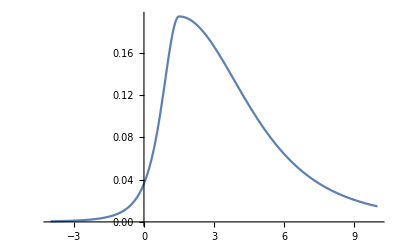

```mathematica
Plot[𝒟/.{d1->3,d2->0.6,μ->4,σ->4},{x,-4,10}]
```

```mathematica
NIntegrate[x 𝒟/.{d1->3,d2->0.6,μ->-4,σ->2},{x,-∞,2}]/NIntegrate[𝒟/.{d1->3,d2->0.6,μ->-4,σ->2},{x,-∞,2}]
```

-4.13821

```mathematica
NIntegrate[𝒟/.{d1->3,d2->0.6,μ->-4,σ->2},{x,-∞,-5.4}]
```

0.143205

```mathematica
ClearAll["Global`*"]
```

```mathematica
𝒟=Bp Cp (1+((Bp x +Ap)/(1+d2))^2 1/(d1-2))^(-(1+d1)/2)
```

Bp Cp (1+(Ap+Bp x)^2/((-2+d1) (1+d2)^2))^(1/2 (-1-d1))

```mathematica
𝒟1=Solve[Eliminate[a==𝒟&&z==(Bp x +Ap)/(1+d2),{x}][[1]],a][[1,1,2]]//Quiet
```

(Bp Cp (1-z^2/(2-d1))^(-d1/2))/(√((-2+d1+z^2)/(-2+d1)))

```mathematica
Qr= (Bp x +Ap)/(1+d2)/.x->Q
```

(Ap+Bp Q)/(1+d2)

```mathematica
IntegralRight=Integrate[z 𝒟1,{z,-Ap/Bp,Qr},Assumptions->{d1>2,d2<1,d2>-1,Cp∈Reals,z∈Reals,Ap∈Reals,Bp∈Reals}]
```

ConditionalExpression[(Bp Cp (-2+d1)^((1+d1)/2) (-(1+d2)^d1 (Ap+Bp Q)^(1-d1) (1+((-2+d1) (1+d2)^2)/(Ap+Bp Q)^2)^((1-d1)/2)+(Ap^2+Bp^2 (-2+d1))^((1-d1)/2) (1+d2) Abs[Bp]^(-1+d1)))/((-1+d1) (1+d2)), ]

```mathematica
IntegralRightFull=IntegralRight/.{Cp-> Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2))),Ap-> 4 d2 Cp (d1-2)/(d1-1)/.Cp-> Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2))),Bp-> √(1+3 d2^2-Ap^2)/.Ap-> 4 d2 Cp (d1-2)/(d1-1)/.Cp-> Gamma[(d1+1)/2]/(Gamma[d1/2] √(π(d1-2)))}
```

ConditionalExpression[((-2+d1)^(-1/2+(1+d1)/2) Gamma[(1+d1)/2] √(1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)) ((1+d2) Abs[1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)]^(1/2 (-1+d1)) ((16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)+(-2+d1) (1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)))^((1-d1)/2)-(1+d2)^d1 ((4 √(-2+d1) d2 Gamma[(1+d1)/2])/((-1+d1) √π Gamma[d1/2])+Q √(1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)))^(1-d1) (1+((-2+d1) (1+d2)^2)/(((4 √(-2+d1) d2 Gamma[(1+d1)/2])/((-1+d1) √π Gamma[d1/2])+Q √(1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)))^2))^((1-d1)/2)))/((-1+d1) (1+d2) √π Gamma[d1/2]), ]

```mathematica
Simplify[π^(1/2 (-3+d1)) Abs[1+3 d2^2-(4 (-2+d1) d2^2 Gamma[1/2 (-1+d1)]^2)/(π Gamma[d1/2]^2)]^(1/2 (-1+d1)) ((-1+d1) Gamma[d1/2])^(-3+d1) Gamma[(1+d1)/2] ((-1+d1)^2 (1+3 d2^2) π Gamma[d1/2]^2-16 (-3+d1) d2^2 Gamma[(1+d1)/2]^2)^((1-d1)/2) √((-2+d1) ((-1+d1)^2 (1+3 d2^2) π Gamma[d1/2]^2-16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2))+IntegralRightFull,Assumptions->{d1>2,d2<1,d2>-1}]
```

ConditionalExpression[π^(1/2 (-3+d1)) Abs[1+3 d2^2-(4 (-2+d1) d2^2 Gamma[1/2 (-1+d1)]^2)/(π Gamma[d1/2]^2)]^(1/2 (-1+d1)) ((-1+d1) Gamma[d1/2])^(-3+d1) Gamma[(1+d1)/2] ((-1+d1)^2 (1+3 d2^2) π Gamma[d1/2]^2-16 (-3+d1) d2^2 Gamma[(1+d1)/2]^2)^((1-d1)/2) √((-2+d1) ((-1+d1)^2 (1+3 d2^2) π Gamma[d1/2]^2-16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2))+((-2+d1)^(d1/2) Gamma[(1+d1)/2] √(1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)) ((1+d2) π^(1/2 (-1+d1)) (((-1+d1)^2 Gamma[d1/2]^2 (1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)))/((-2+d1) ((-1+d1)^2 (1+3 d2^2) π Gamma[d1/2]^2-16 (-3+d1) d2^2 Gamma[(1+d1)/2]^2)))^(1/2 (-1+d1))-(1+d2)^d1 ((4 √(-2+d1) d2 Gamma[(1+d1)/2])/((-1+d1) √π Gamma[d1/2])+Q √(1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)))^(1-d1) (1+((-2+d1) (1+d2)^2)/(((4 √(-2+d1) d2 Gamma[(1+d1)/2])/((-1+d1) √π Gamma[d1/2])+Q √(1+3 d2^2-(16 (-2+d1) d2^2 Gamma[(1+d1)/2]^2)/((-1+d1)^2 π Gamma[d1/2]^2)))^2))^((1-d1)/2)))/((-1+d1) (1+d2) √π Gamma[d1/2]), ]